# pubmed data analysis top pubyear 1946-2020: window=5,wrap=0

## Summary/Report

### definition

```mathematica
Get["/Volumes/elecom/BANK/pubmed/202312/exec_command/defs.wl"]//TableForm
```

主要論文 | 被引用数全体の1%を構成する被引用数上位論文（集合）。
主要雑誌 | 主要論文を出版した雑誌。
主要テーマ | 主要論文に付与されるMeSH。
世代 | 1946 - 2020の期間に対して5年ごとに区切るもの。データを累積的に扱う場合は「累積世代」と表記する。

### generation

```mathematica
Get["/Volumes/elecom/BANK/pubmed/202312/exec_command/generations.wl"]
```

{1950,1955,1960,1965,1970,1975,1980,1985,1990,1995,2000,2005,2010,2015,2020}

```mathematica
period
```

{1950,1955,1960,1965,1970,1975,1980,1985,1990,1995,2000,2005,2010,2015,2020}

```mathematica
periodticks
```

{{1,1950},{2,1955},{3,1960},{4,1965},{5,1970},{6,1975},{7,1980},{8,1985},{9,1990},{10,1995},{11,2000},{12,2005},{13,2010},{14,2015},{15,2020}}

```mathematica
gen
```

{1946-1950,1946-1955,1946-1960,1946-1965,1946-1970,1946-1975,1946-1980,1946-1985,1946-1990,1946-1995,1946-2000,1946-2005,1946-2010,1946-2015,1946-2020}

```mathematica
genR
```

{1946-1950,1946-1955,1946-1960,1946-1965,1946-1970,1946-1975,1946-1980,1946-1985,1946-1990,1946-1995,1946-2000,1946-2005,1946-2010,1946-2015,1946-2020}

```mathematica
genticks
```

{{1,1946-1950},{2,1946-1955},{3,1946-1960},{4,1946-1965},{5,1946-1970},{6,1946-1975},{7,1946-1980},{8,1946-1985},{9,1946-1990},{10,1946-1995},{11,1946-2000},{12,1946-2005},{13,1946-2010},{14,1946-2015},{15,1946-2020}}

```mathematica
genEnd
```

{1950,1955,1960,1965,1970,1975,1980,1985,1990,1995,2000,2005,2010,2015,2020}

### cited article rank vs. cited points (fit to Zipf : zipf[r_]:=c r^(-a)) (1950 ~ 2020)

```mathematica
zipffit[1950]={c->78.76503658791894,a->0.43312539741347483}
zipffit[1955]={c->198.79897660125383,a->0.44227503637989046}
zipffit[1960]={c->391.41395908279713,a->0.4567333859884886}
zipffit[1965]={c->821.3098544459095,a->0.4916116216009761}
zipffit[1970]={c->2269.503111758494,a->0.5624150871452113}
zipffit[1975]={c->5698.629066933866,a->0.6474958575641221}
zipffit[1980]={c->12604.089717142908,a->0.8120519133189623}
zipffit[1985]={c->19129.603616538705,a->0.7879887594004762}
zipffit[1990]={c->27447.37619157219,a->0.7466622275538692}
zipffit[1995]={c->35550.46262361971,a->0.7220751829539006}
zipffit[2000]={c->39613.680986874926,a->0.7005635105242737}
zipffit[2005]={c->41226.43325006025,a->0.6709088827836299}
zipffit[2010]={c->42654.289511746094,a->0.6097890504842925}
zipffit[2015]={c->52142.058384605836,a->0.5610957676644441}
zipffit[2020]={c->72848.30291399686,a->0.5437053248879677}
```

{c→78.765,a→0.433125}

{c→198.799,a→0.442275}

{c→391.414,a→0.456733}

{c→821.31,a→0.491612}

{c→2269.5,a→0.562415}

{c→5698.63,a→0.647496}

{c→12604.1,a→0.812052}

{c→19129.6,a→0.787989}

{c→27447.4,a→0.746662}

{c→35550.5,a→0.722075}

{c→39613.7,a→0.700564}

{c→41226.4,a→0.670909}

{c→42654.3,a→0.609789}

{c→52142.1,a→0.561096}

{c→72848.3,a→0.543705}

```mathematica
zipffitTbl=Table[zipffit[n],{n,1950,2020,5}]
```

{{c→78.765,a→0.433125},{c→198.799,a→0.442275},{c→391.414,a→0.456733},{c→821.31,a→0.491612},{c→2269.5,a→0.562415},{c→5698.63,a→0.647496},{c→12604.1,a→0.812052},{c→19129.6,a→0.787989},{c→27447.4,a→0.746662},{c→35550.5,a→0.722075},{c→39613.7,a→0.700564},{c→41226.4,a→0.670909},{c→42654.3,a→0.609789},{c→52142.1,a→0.561096},{c→72848.3,a→0.543705}}

```mathematica
zipffitTbla=Map[Round[#[[2,2]],0.01]&,zipffitTbl]
```

{0.43,0.44,0.46,0.49,0.56,0.65,0.81,0.79,0.75,0.72,0.7,0.67,0.61,0.56,0.54}

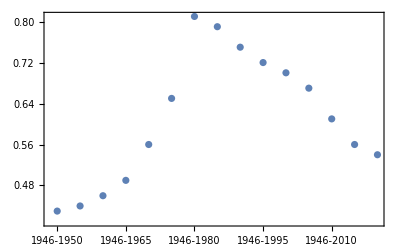

```mathematica
tbl5=ListPlot[zipffitTbla,Frame->True,FrameTicks->{Automatic,{genticks,None}},PlotRange->Full]
```

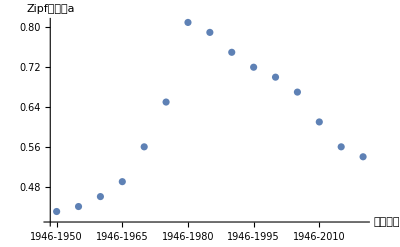

```mathematica
tbl5=ListPlot[zipffitTbla,PlotRange->Full,AxesLabel->{"累積世代","Zipfの係数a"},Ticks->{genticks,Automatic}]
```

### count of lone node (no-ref, no-cited, not WCG) (1950 ~ 2020)

```mathematica
loneArtFiles=FileNames["/Volumes/elecom/BANK/pubmed/202312/xml/element/reference/lonearticle*wl"]
```

{/Volumes/elecom/BANK/pubmed/202312/xml/element/reference/lonearticle_1946-1950.wl,/Volumes/elecom/BANK/pubmed/202312/xml/element/reference/lonearticle_1946-1955.wl,/Volumes/elecom/BANK/pubmed/202312/xml/element/reference/lonearticle_1946-1960.wl,/Volumes/elecom/BANK/pubmed/202312/xml/element/reference/lonearticle_1946-1965.wl,/Volumes/elecom/BANK/pubmed/202312/xml/element/reference/lonearticle_1946-1970.wl,/Volumes/elecom/BANK/pubmed/202312/xml/element/reference/lonearticle_1946-1975.wl,/Volumes/elecom/BANK/pubmed/202312/xml/element/reference/lonearticle_1946-1980.wl,/Volumes/elecom/BANK/pubmed/202312/xml/element/reference/lonearticle_1946-1985.wl,/Volumes/elecom/BANK/pubmed/202312/xml/element/reference/lonearticle_1946-1990.wl,/Volumes/elecom/BANK/pubmed/202312/xml/element/reference/lonearticle_1946-1995.wl,/Volumes/elecom/BANK/pubmed/202312/xml/element/reference/lonearticle_1946-2000.wl,/Volumes/elecom/BANK/pubmed/202312/xml/element/reference/lonearticle_1946-2005.wl,/Volumes/elecom/BANK/pubmed/202312/xml/element/reference/lonearticle_1946-2010.wl,/Volumes/elecom/BANK/pubmed/202312/xml/element/reference/lonearticle_1946-2015.wl,/Volumes/elecom/BANK/pubmed/202312/xml/element/reference/lonearticle_1946-2020.wl}

```mathematica
loneArticles=Map[Get,loneArtFiles];
```

```mathematica
loneArtCount=Map[Length,loneArticles]
```

{296336,774662,1203519,1774556,2542940,3356424,4248958,5222321,6403037,7594669,9000206,10294609,10857321,11071404,11229183}

### basic graph properties (1950 ~ 2020)

```mathematica
wcgprofiles=FileNames["/Volumes/elecom/BANK/pubmed/202312/xml/element/reference/*_wcgproperty.save"]
```

{/Volumes/elecom/BANK/pubmed/202312/xml/element/reference/1946-1950_wcgproperty.save,/Volumes/elecom/BANK/pubmed/202312/xml/element/reference/1946-1955_wcgproperty.save,/Volumes/elecom/BANK/pubmed/202312/xml/element/reference/1946-1960_wcgproperty.save,/Volumes/elecom/BANK/pubmed/202312/xml/element/reference/1946-1965_wcgproperty.save,/Volumes/elecom/BANK/pubmed/202312/xml/element/reference/1946-1970_wcgproperty.save,/Volumes/elecom/BANK/pubmed/202312/xml/element/reference/1946-1975_wcgproperty.save,/Volumes/elecom/BANK/pubmed/202312/xml/element/reference/1946-1980_wcgproperty.save,/Volumes/elecom/BANK/pubmed/202312/xml/element/reference/1946-1985_wcgproperty.save,/Volumes/elecom/BANK/pubmed/202312/xml/element/reference/1946-1990_wcgproperty.save,/Volumes/elecom/BANK/pubmed/202312/xml/element/reference/1946-1995_wcgproperty.save,/Volumes/elecom/BANK/pubmed/202312/xml/element/reference/1946-2000_wcgproperty.save,/Volumes/elecom/BANK/pubmed/202312/xml/element/reference/1946-2005_wcgproperty.save,/Volumes/elecom/BANK/pubmed/202312/xml/element/reference/1946-2010_wcgproperty.save,/Volumes/elecom/BANK/pubmed/202312/xml/element/reference/1946-2015_wcgproperty.save,/Volumes/elecom/BANK/pubmed/202312/xml/element/reference/1946-2020_wcgproperty.save}

```mathematica
Map[Get,wcgprofiles]//Length
```

15

Total vertex

```mathematica
totalV=Map[vctotal[#]&,gen]
```

{25659,106865,230664,387646,635815,991194,1452803,2022734,2761367,3715190,4704818,6388248,9604916,14351433,20271870}

```mathematica
grandtotalV=totalV+loneArtCount
```

{321995,881527,1434183,2162202,3178755,4347618,5701761,7245055,9164404,11309859,13705024,16682857,20462237,25422837,31501053}

```mathematica
loneArtPercent=loneArtCount/grandtotalV*100//N
```

{92.0312,87.8773,83.9167,82.0717,79.998,77.2014,74.5201,72.0812,69.8686,67.1509,65.6709,61.7077,53.0603,43.5491,35.647}

Total edge

```mathematica
totalE=Map[Total[ec[#]]&,gen]
```

{33832,182387,474042,919064,1737693,3107381,5106059,7927708,11950422,17666111,23761602,33378392,61234426,124935745,223840771}

WCG count

```mathematica
wcgN=Map[wcgcount[#]&,gen]
```

{2353,3851,4624,5729,7020,8446,9401,10026,10687,11361,12147,13000,13398,13643,14933}

Max WCG vertex count

```mathematica
wcgVmax=Map[vcmax[#]&,gen]
```

{17910,94830,216474,370660,615244,966113,1425267,1993398,2730892,3683220,4670358,6351561,9568400,14315982,20235562}

Max WCG vertex count %

```mathematica
wcgVmaxperc=Round[Map[vcmax[#]&,gen]/Map[vctotal[#]&,gen]*100//N,0.1]
```

{69.8,88.7,93.8,95.6,96.8,97.5,98.1,98.5,98.9,99.1,99.3,99.4,99.6,99.8,99.8}

Max WCG vertex count % (from all articles)

```mathematica
wcgVmaxpercAll=Round[Map[vcmax[#]&,gen]/cumulativeArtcount*100//N,0.1]
```

{5.4,10.9,15.3,17.3,19.5,22.3,25.1,27.6,29.9,32.7,34.2,38.2,46.9,56.4,64.4}

Cyclomatic Complexity

```mathematica
cyclomaticTri={totalE,totalV,wcgN}//Transpose
```

{{33832,25659,2353},{182387,106865,3851},{474042,230664,4624},{919064,387646,5729},{1737693,635815,7020},{3107381,991194,8446},{5106059,1452803,9401},{7927708,2022734,10026},{11950422,2761367,10687},{17666111,3715190,11361},{23761602,4704818,12147},{33378392,6388248,13000},{61234426,9604916,13398},{124935745,14351433,13643},{223840771,20271870,14933}}

```mathematica
complexity=Map[cyclomaticComolexity,cyclomaticTri]
```

{12879,83224,252626,542876,1115918,2133079,3672058,5925026,9210429,13973643,19081078,27016144,51656306,110611598,203598767}

Zipf' s "a"

```mathematica
zipfa=Round[Map[vcZipfParam[#][[2,2]]&,gen],0.01]
```

{7.51,11.26,12.1,13.4,13.94,13.13,13.7,14.18,14.7,15.4,15.4,17.27,17.87,18.64,19.1}

Table

```mathematica
wcgtblhead={"Generation","WCG","WCG vertices","WCG edges","Lone vertices","Largest WCG vertices","Largest WCG vertices %","Largest WCG vertices % (all articles)","complexity","Zipf's a"}
```

{Generation,WCG,WCG vertices,WCG edges,Lone vertices,Largest WCG vertices,Largest WCG vertices %,Largest WCG vertices % (all articles),complexity,Zipf's a}

```mathematica
wcgtblheadJ={"累積世代","WCG数","連結ノード総数","エッジ総数","孤立ノード数","最大WCGノード数","最大WCGノード %","最大WCGノード % (孤立ノード含)","複雑性","Zipfの係数a"}
```

{累積世代,WCG数,連結ノード総数,エッジ総数,孤立ノード数,最大WCGノード数,最大WCGノード %,最大WCGノード % (孤立ノード含),複雑性,Zipfの係数a}

```mathematica
wcgtblval={wcgN,totalV,totalE,loneArtCount,wcgVmax,wcgVmaxperc,wcgVmaxpercAll,complexity,zipfa}
```

{{2353,3851,4624,5729,7020,8446,9401,10026,10687,11361,12147,13000,13398,13643,14933},{25659,106865,230664,387646,635815,991194,1452803,2022734,2761367,3715190,4704818,6388248,9604916,14351433,20271870},{33832,182387,474042,919064,1737693,3107381,5106059,7927708,11950422,17666111,23761602,33378392,61234426,124935745,223840771},{296336,774662,1203519,1774556,2542940,3356424,4248958,5222321,6403037,7594669,9000206,10294609,10857321,11071404,11229183},{17910,94830,216474,370660,615244,966113,1425267,1993398,2730892,3683220,4670358,6351561,9568400,14315982,20235562},{69.8,88.7,93.8,95.6,96.8,97.5,98.1,98.5,98.9,99.1,99.3,99.4,99.6,99.8,99.8},{5.4,10.9,15.3,17.3,19.5,22.3,25.1,27.6,29.9,32.7,34.2,38.2,46.9,56.4,64.4},{12879,83224,252626,542876,1115918,2133079,3672058,5925026,9210429,13973643,19081078,27016144,51656306,110611598,203598767},{7.51,11.26,12.1,13.4,13.94,13.13,13.7,14.18,14.7,15.4,15.4,17.27,17.87,18.64,19.1}}

```mathematica
(wcgtblJ=Prepend[Transpose[{gen,wcgN,totalV,totalE,loneArtCount,wcgVmax,wcgVmaxperc,wcgVmaxpercAll,complexity,zipfa}],wcgtblheadJ])//TableForm
```

累積世代 | WCG数 | 連結ノード総数 | エッジ総数 | 孤立ノード数 | 最大WCGノード数 | 最大WCGノード % | 最大WCGノード % (孤立ノード含) | 複雑性 | Zipfの係数a
1946-1950 | 2353 | 25659 | 33832 | 296336 | 17910 | 69.8 | 5.4 | 12879 | 7.51
1946-1955 | 3851 | 106865 | 182387 | 774662 | 94830 | 88.7 | 10.9 | 83224 | 11.26
1946-1960 | 4624 | 230664 | 474042 | 1203519 | 216474 | 93.8 | 15.3 | 252626 | 12.1
1946-1965 | 5729 | 387646 | 919064 | 1774556 | 370660 | 95.6 | 17.3 | 542876 | 13.4
1946-1970 | 7020 | 635815 | 1737693 | 2542940 | 615244 | 96.8 | 19.5 | 1115918 | 13.94
1946-1975 | 8446 | 991194 | 3107381 | 3356424 | 966113 | 97.5 | 22.3 | 2133079 | 13.13
1946-1980 | 9401 | 1452803 | 5106059 | 4248958 | 1425267 | 98.1 | 25.1 | 3672058 | 13.7
1946-1985 | 10026 | 2022734 | 7927708 | 5222321 | 1993398 | 98.5 | 27.6 | 5925026 | 14.18
1946-1990 | 10687 | 2761367 | 11950422 | 6403037 | 2730892 | 98.9 | 29.9 | 9210429 | 14.7
1946-1995 | 11361 | 3715190 | 17666111 | 7594669 | 3683220 | 99.1 | 32.7 | 13973643 | 15.4
1946-2000 | 12147 | 4704818 | 23761602 | 9000206 | 4670358 | 99.3 | 34.2 | 19081078 | 15.4
1946-2005 | 13000 | 6388248 | 33378392 | 10294609 | 6351561 | 99.4 | 38.2 | 27016144 | 17.27
1946-2010 | 13398 | 9604916 | 61234426 | 10857321 | 9568400 | 99.6 | 46.9 | 51656306 | 17.87
1946-2015 | 13643 | 14351433 | 124935745 | 11071404 | 14315982 | 99.8 | 56.4 | 110611598 | 18.64
1946-2020 | 14933 | 20271870 | 223840771 | 11229183 | 20235562 | 99.8 | 64.4 | 203598767 | 19.1

```mathematica
ListPlot[wcgtblval,Joined->True,PlotRange->Full,Ticks->{genticks,Automatic},PlotLabels->wcgtblheadJ[[2;;]],AxesLabel->{"累積世代","カウント"}]
```

-Graphics-

```mathematica
wcgpltheadJ={"累積世代","WCG数","連結ノード総数","エッジ総数","孤立ノード数","最大WCGノード数","複雑性"}
```

{累積世代,WCG数,連結ノード総数,エッジ総数,孤立ノード数,最大WCGノード数,複雑性}

```mathematica
(wcgpltval={wcgN,totalV,totalE,loneArtCount,wcgVmax,complexity})//TableForm
```

2353 | 3851 | 4624 | 5729 | 7020 | 8446 | 9401 | 10026 | 10687 | 11361 | 12147 | 13000 | 13398 | 13643 | 14933
25659 | 106865 | 230664 | 387646 | 635815 | 991194 | 1452803 | 2022734 | 2761367 | 3715190 | 4704818 | 6388248 | 9604916 | 14351433 | 20271870
33832 | 182387 | 474042 | 919064 | 1737693 | 3107381 | 5106059 | 7927708 | 11950422 | 17666111 | 23761602 | 33378392 | 61234426 | 124935745 | 223840771
296336 | 774662 | 1203519 | 1774556 | 2542940 | 3356424 | 4248958 | 5222321 | 6403037 | 7594669 | 9000206 | 10294609 | 10857321 | 11071404 | 11229183
17910 | 94830 | 216474 | 370660 | 615244 | 966113 | 1425267 | 1993398 | 2730892 | 3683220 | 4670358 | 6351561 | 9568400 | 14315982 | 20235562
12879 | 83224 | 252626 | 542876 | 1115918 | 2133079 | 3672058 | 5925026 | 9210429 | 13973643 | 19081078 | 27016144 | 51656306 | 110611598 | 203598767

```mathematica
ListPlot[wcgpltval,Joined->True,PlotRange->Full,Ticks->{genticks,Automatic},PlotLabels->wcgpltheadJ[[2;;]],AxesLabel->{"累積世代","カウント"}]
```

-Graphics-

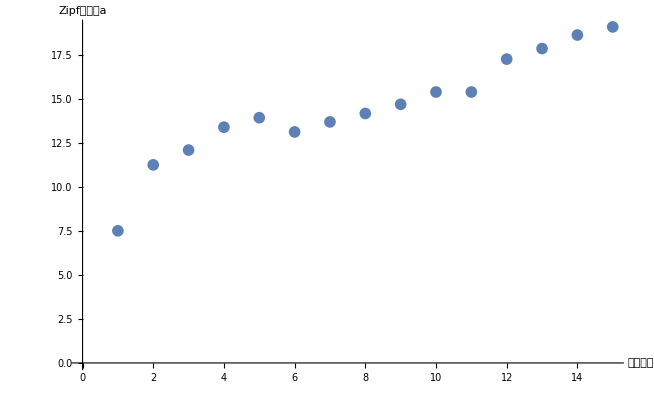

```mathematica
ListPlot[zipfa,AxesLabel->{"累積世代","Zipfの係数a"}]
```

```mathematica
percentHead={"最大WCGノード %","最大WCGノード % (孤立ノード含)","孤立ノード %"}
```

{最大WCGノード %,最大WCGノード % (孤立ノード含),孤立ノード %}

```mathematica
ListPlot[{wcgtblval[[6]],wcgtblval[[7]],loneArtPercent},Joined->True,PlotRange->Full,Ticks->{genticks,Automatic},PlotLabels->percentHead,AxesLabel->{"累積世代","%"}]
```

-Graphics-

### graph elongation (1950 ~ 2020)

```mathematica
Get["/Volumes/elecom/BANK/pubmed/202312/xml/element/reference/graphDiff.save"];
```

A. 新規に発生した引用数*

```mathematica
newedgecountAll=Table[newedgecount[n],{n,1955,2020,5}]
```

{148555,291655,445022,818629,1369688,1998678,2821649,4022714,5715688,6095490,9616785,27854672,63696093,98878679}

B-3 新規に発生した引用のうちtop1%論文に対する引用数

```mathematica
newedgecounttop1percAll=Table[newedgecounttop1perc[n],{n,1955,2020,5}]
```

{304,1235,2835,9219,14013,17085,26144,50019,45096,30524,21803,44967,268426,676422}

```mathematica
newedgecounttop1percAllratio=Round[newedgecounttop1percAll/newedgecountAll//N,0.001]*100
```

{0.2,0.4,0.6,1.1,1.,0.9,0.9,1.2,0.8,0.5,0.2,0.2,0.4,0.7}

```mathematica
newedgecounttop1percAlltbl=Table[ToString[newedgecounttop1percAll[[n]]]<>" ("<>ToString[newedgecounttop1percAllratio[[n]]]<>")",{n,14}]
```

{304 (0.2),1235 (0.4),2835 (0.6),9219 (1.1),14013 (1.),17085 (0.9),26144 (0.9),50019 (1.2),45096 (0.8),30524 (0.5),21803 (0.2),44967 (0.2),268426 (0.4),676422 (0.7)}

A - 1. 新規に発生した引用により結合が発生した前世代WCG数*

```mathematica
newconnectedWCGcountAll=Table[newconnectedWCGcount[n],{n,1955,2020,5}]
```

{1280,1485,1297,1411,1549,1716,1683,1553,1450,1147,1508,2576,3404,3472}

A-3. 新規に発生した引用に関して異なる前世代WCGを結合する論文の数*

```mathematica
newMetaconnectedArtcountAll=Table[newMetaconnectedArtcount[n],{n,1955,2020,5}]
```

{1632,1942,1717,1937,2240,2520,2480,2438,2345,1603,2553,6243,11124,11676}

A-4. 新規に発生した引用により異なる前世代WCGと結合された前世代WCG数*

```mathematica
newMetaconnectedWCGcountAll=Table[newMetaconnectedWCGcount[n],{n,1955,2020,5}]
```

{909,1185,1070,1133,1306,1500,1478,1392,1310,1048,1353,2407,3235,3255}

WCGの結合率*

```mathematica
WCGconnectedRatio=Round[newMetaconnectedWCGcountAll/wcgN[[;;-2]]//N,0.01]
```

{0.39,0.31,0.23,0.2,0.19,0.18,0.16,0.14,0.12,0.09,0.11,0.19,0.24,0.24}

```mathematica
WCGcongen=Table[n,{n,1955,2020,5}]
```

{1955,1960,1965,1970,1975,1980,1985,1990,1995,2000,2005,2010,2015,2020}

```mathematica
elgTblHead={"累積世代","新規に発生した引用数","新規に発生した引用のうち\n主要論文に対する引用数(%)","新規に発生した引用に関して\n異なる前世代WCGを結合する論文の数","新規に発生した引用により\n結合が発生した前世代WCG数","新規に発生した引用により\n異なる前世代WCGと結合された前世代WCG数","前世代WCG数","WCGの結合率"}
```

{累積世代,新規に発生した引用数,新規に発生した引用のうち
主要論文に対する引用数(%),新規に発生した引用に関して
異なる前世代WCGを結合する論文の数,新規に発生した引用により
結合が発生した前世代WCG数,新規に発生した引用により
異なる前世代WCGと結合された前世代WCG数,前世代WCG数,WCGの結合率}

```mathematica
Prepend[Transpose[{WCGcongen,newedgecountAll,newedgecounttop1percAlltbl,newMetaconnectedArtcountAll,newconnectedWCGcountAll,newMetaconnectedWCGcountAll,wcgN[[;;-2]],WCGconnectedRatio}],elgTblHead]//TableForm
```

累積世代 | 新規に発生した引用数 | 新規に発生した引用のうち
主要論文に対する引用数(%) | 新規に発生した引用に関して
異なる前世代WCGを結合する論文の数 | 新規に発生した引用により
結合が発生した前世代WCG数 | 新規に発生した引用により
異なる前世代WCGと結合された前世代WCG数 | 前世代WCG数 | WCGの結合率
1955 | 148555 | 304 (0.2) | 1632 | 1280 | 909 | 2353 | 0.39
1960 | 291655 | 1235 (0.4) | 1942 | 1485 | 1185 | 3851 | 0.31
1965 | 445022 | 2835 (0.6) | 1717 | 1297 | 1070 | 4624 | 0.23
1970 | 818629 | 9219 (1.1) | 1937 | 1411 | 1133 | 5729 | 0.2
1975 | 1369688 | 14013 (1.) | 2240 | 1549 | 1306 | 7020 | 0.19
1980 | 1998678 | 17085 (0.9) | 2520 | 1716 | 1500 | 8446 | 0.18
1985 | 2821649 | 26144 (0.9) | 2480 | 1683 | 1478 | 9401 | 0.16
1990 | 4022714 | 50019 (1.2) | 2438 | 1553 | 1392 | 10026 | 0.14
1995 | 5715688 | 45096 (0.8) | 2345 | 1450 | 1310 | 10687 | 0.12
2000 | 6095490 | 30524 (0.5) | 1603 | 1147 | 1048 | 11361 | 0.09
2005 | 9616785 | 21803 (0.2) | 2553 | 1508 | 1353 | 12147 | 0.11
2010 | 27854672 | 44967 (0.2) | 6243 | 2576 | 2407 | 13000 | 0.19
2015 | 63696093 | 268426 (0.4) | 11124 | 3404 | 3235 | 13398 | 0.24
2020 | 98878679 | 676422 (0.7) | 11676 | 3472 | 3255 | 13643 | 0.24

Visualization

```mathematica
withG[currentList_List,currentG_Integer]:=Module[{len,prevG},
prevG=currentG-5;
len=Length[currentList];
Table[Map[prevG[#]->currentG[n]&,currentList[[n]]],{n,len}]
]
```

```mathematica
WCGlinkwithG[currentList_List,currentG_Integer]:=Tally[Flatten[withG[currentList,currentG]]]
```

```mathematica
WCGlinkToGraph[link_]:=Graph[Map[DirectedEdge[#[[1,1]],#[[1,2]],#[[2]]]&,link]]
```

```mathematica
refdatadir="/Volumes/elecom/BANK/pubmed/202312/xml/element/reference/"
```

/Volumes/elecom/BANK/pubmed/202312/xml/element/reference/

```mathematica
datafile="elongationMat.save"
```

elongationMat.save

```mathematica
Do[WCGcount[genEnd[[n]]]=wcgN[[n]],{n,1,15}]
```

```mathematica
wcgsavefile="WCGELinkAll.save"
```

WCGELinkAll.save

```mathematica
Get[refdatadir<>wcgsavefile];
```

```mathematica
WCGElink[10]=Cases[WCGElink["All"],x_/;x[[2]]>=10];
```

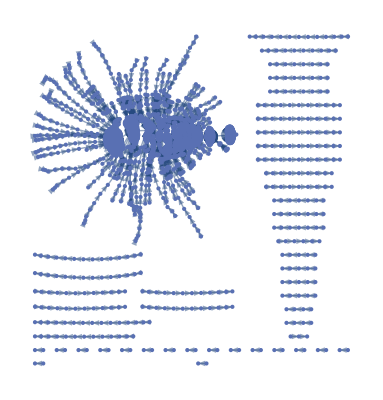

```mathematica
WCGelgraph[10]=WCGlinkToGraph[WCGElink[10]]
```

```mathematica
vc10=Map[#->{#[[0]],#[[1]]/WCGcount[#[[0]]]*100}&,WCGelgraph[10]//VertexList];
```

```mathematica
max=Map[N[#[[3]]]&,EdgeList[WCGelgraph[10]]]//Max
min=Map[N[#[[3]]]&,EdgeList[WCGelgraph[10]]]//Min
```

1.99873×10^8

10.

```mathematica
myColors={Red,RGBColor[1,0.5,0],RGBColor[0.9,0.8,0],RGBColor[0.3,0.6,1]}
```

{RGBColor[1, 0, 0],RGBColor[1, 0.5, 0],RGBColor[0.9, 0.8, 0],RGBColor[0.3, 0.6, 1]}

```mathematica
myColorData[v_]:=Which[v>=45,Red,45>v&&v>=25,RGBColor[1,0.5,0],25>v&&v>=15,RGBColor[0.9,0.8,0], 15>v&&v>=10,RGBColor[0.3,0.6,1]]
```

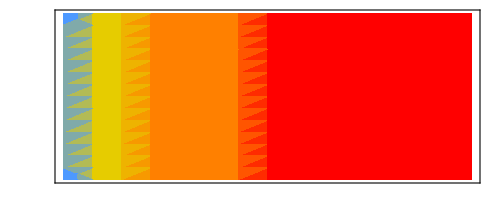
-Graphics-
弱    <-結合->    強

```mathematica
colorscale=Grid[{{DensityPlot[x,{x,min,80},{y,0,10},ColorFunction->myColorData,ColorFunctionScaling->False,AspectRatio->Automatic,FrameTicks->{{None,None},{None,None}}]},{"弱    <-結合->    強"}}]
```

```mathematica
es=Table[EdgeList[WCGelgraph[10]][[n]]->myColorData[(EdgeList[WCGelgraph[10]][[n]][[3]])],{n,Length[EdgeList[WCGelgraph[10]]]}]
```

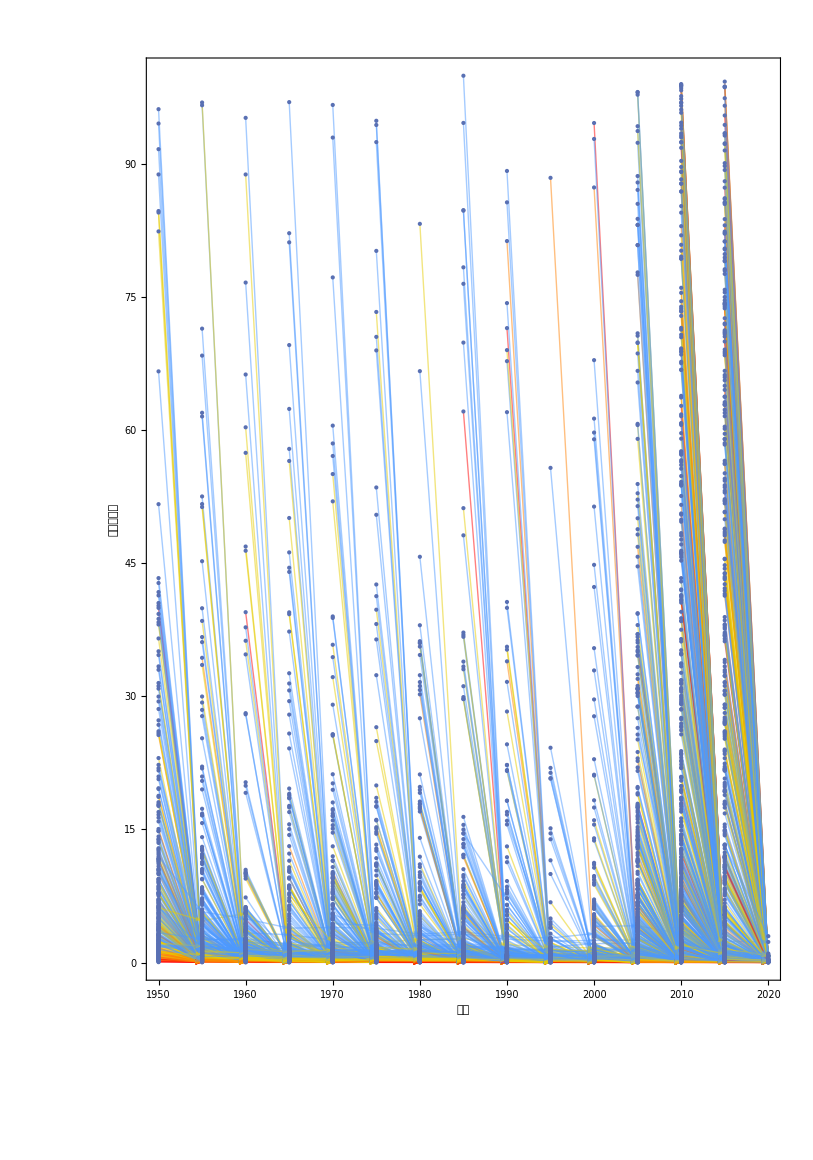

```mathematica
gp10=GraphPlot[Graph[WCGelgraph[10],VertexCoordinates->vc10,EdgeStyle->es,Frame->True,FrameTicks->{Automatic,Automatic}],FrameLabel->{"世代","順位百分率"}]
```

Edge proportion

```mathematica
epTbl=Table[Counts[Map[#[[2]]&,Cases[es,x_/;Head[x[[1,1]]]==(n-5)&&Head[x[[1,2]]]==n]]],{n,1955,2020,5}]
```

{<|RGBColor[0.9, 0.8, 0]→72,RGBColor[1, 0, 0]→13,RGBColor[0.3, 0.6, 1]→115,RGBColor[1, 0.5, 0]→27|>,<|RGBColor[1, 0, 0]→4,RGBColor[0.3, 0.6, 1]→127,RGBColor[0.9, 0.8, 0]→59,RGBColor[1, 0.5, 0]→18|>,<|RGBColor[1, 0, 0]→5,RGBColor[0.3, 0.6, 1]→103,RGBColor[0.9, 0.8, 0]→59,RGBColor[1, 0.5, 0]→10|>,<|RGBColor[1, 0, 0]→4,RGBColor[0.3, 0.6, 1]→114,RGBColor[1, 0.5, 0]→11,RGBColor[0.9, 0.8, 0]→61|>,<|RGBColor[1, 0, 0]→3,RGBColor[0.9, 0.8, 0]→75,RGBColor[0.3, 0.6, 1]→128,RGBColor[1, 0.5, 0]→13|>,<|RGBColor[1, 0, 0]→8,RGBColor[0.3, 0.6, 1]→136,RGBColor[0.9, 0.8, 0]→66,RGBColor[1, 0.5, 0]→24|>,<|RGBColor[1, 0, 0]→8,RGBColor[0.3, 0.6, 1]→131,RGBColor[1, 0.5, 0]→21,RGBColor[0.9, 0.8, 0]→71|>,<|RGBColor[1, 0, 0]→11,RGBColor[0.3, 0.6, 1]→148,RGBColor[0.9, 0.8, 0]→70,RGBColor[1, 0.5, 0]→24|>,<|RGBColor[1, 0, 0]→7,RGBColor[0.9, 0.8, 0]→62,RGBColor[0.3, 0.6, 1]→123,RGBColor[1, 0.5, 0]→13|>,<|RGBColor[1, 0, 0]→4,RGBColor[0.3, 0.6, 1]→102,RGBColor[0.9, 0.8, 0]→51,RGBColor[1, 0.5, 0]→9|>,<|RGBColor[1, 0, 0]→10,RGBColor[0.9, 0.8, 0]→71,RGBColor[1, 0.5, 0]→13,RGBColor[0.3, 0.6, 1]→138|>,<|RGBColor[1, 0, 0]→11,RGBColor[0.9, 0.8, 0]→125,RGBColor[1, 0.5, 0]→36,RGBColor[0.3, 0.6, 1]→238|>,<|RGBColor[1, 0, 0]→28,RGBColor[0.3, 0.6, 1]→289,RGBColor[1, 0.5, 0]→61,RGBColor[0.9, 0.8, 0]→163|>,<|RGBColor[1, 0, 0]→33,RGBColor[0.3, 0.6, 1]→227,RGBColor[1, 0.5, 0]→55,RGBColor[0.9, 0.8, 0]→137|>}

```mathematica
myColors
```

{RGBColor[1, 0, 0],RGBColor[1, 0.5, 0],RGBColor[0.9, 0.8, 0],RGBColor[0.3, 0.6, 1]}

```mathematica
colorPerc[asc_]:=Module[{total},
total=Total[asc];
Map[asc,myColors]/total
]
```

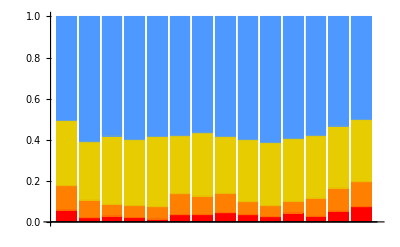

```mathematica
BarChart[Map[colorPerc,epTbl],ChartLayout->"Stacked",ChartStyle->myColors]
```

### WCG connection by top 1% article (1950 ~ 2020)

すべての年代のすべての主要論文が最大WCGに含まれる。

```mathematica
WCGfconBytop1percArt[1955]={{1,321}}
WCGfconBytop1percArt[1960]={{1,1502},{2375,1}}
WCGfconBytop1percArt[1965]={{1,3769}}
WCGfconBytop1percArt[1970]={{1,7092}}
WCGfconBytop1percArt[1975]={{1,13029}}
WCGfconBytop1percArt[1980]={{1,23900}}
WCGfconBytop1percArt[1985]={{1,39260}}
WCGfconBytop1percArt[1990]={{1,58839}}
WCGfconBytop1percArt[1995]={{1,86067}}
WCGfconBytop1percArt[2000]={{1,124936}}
WCGfconBytop1percArt[2005]={{1,161003}}
WCGfconBytop1percArt[2010]={{1,213200}}
WCGfconBytop1percArt[2015]={{1,388123},{2573,2},{9981,1}}
WCGfconBytop1percArt[2020]={{1,786498},{9815,1},{5982,1},{12481,1}}
```

{{1,321}}

{{1,1502},{2375,1}}

{{1,3769}}

{{1,7092}}

{{1,13029}}

{{1,23900}}

{{1,39260}}

{{1,58839}}

{{1,86067}}

{{1,124936}}

{{1,161003}}

{{1,213200}}

{{1,388123},{2573,2},{9981,1}}

{{1,786498},{9815,1},{5982,1},{12481,1}}

```mathematica
WCGbconBytop1percArt[1955]={{1,1663},{1734,1},{1786,1},{1553,1},{1988,2},{345,1},{1641,1},{497,1},{863,1},{1314,1},{1934,1},{1938,1},{1992,2},{185,1},{47,1},{91,2},{2064,1},{2182,1},{348,1},{613,1},{544,1}}
WCGbconBytop1percArt[1960]={{1,10564},{3219,1},{135,1},{3363,1},{751,1},{212,3},{2375,1},{1611,1},{3731,2},{168,1},{3710,1},{1547,1},{1089,1},{1128,1},{55,1},{2052,1},{1390,2},{189,1},{576,1},{3293,1},{1322,1},{921,1},{2398,1},{3591,1},{646,1},{1981,1},{312,1},{1328,1},{1818,1},{3796,1},{489,1},{704,1},{81,1},{2022,1}}
WCGbconBytop1percArt[1965]={{1,32520},{1189,1},{1676,1},{224,2},{3057,1},{3024,1},{2700,1},{4609,1},{1652,1},{1955,1},{4105,1},{393,1},{1825,1},{1538,1},{1746,1},{705,1},{625,1},{1202,1},{1598,1},{1263,1},{643,1},{1212,1},{3009,1},{156,1},{9,1},{1176,1},{3542,2},{2259,1},{2788,1},{1738,1},{1234,1},{1546,1},{3170,1},{3641,2},{458,1},{3343,1},{3590,1},{3664,2},{384,1},{222,1},{2167,1},{2544,1},{100,3},{2655,2},{2748,1},{2734,1}}
WCGbconBytop1percArt[1970]={{1,64232},{1936,1},{4707,1},{199,3},{3684,1},{4648,1},{3889,1},{1982,1},{3069,1},{856,1},{338,3},{2260,3},{2548,2},{4681,1},{4550,1},{2310,1},{2116,1},{2973,1},{837,1},{1365,1},{4164,1},{2066,1},{1089,1},{2952,1},{4078,1},{283,1},{3237,1},{5391,1},{3308,1},{1180,1},{1071,1},{210,1},{122,1},{541,1},{1727,1},{2801,1},{4305,2},{685,1},{5216,1},{4615,1},{4345,2},{1300,1},{1226,1},{4036,1},{508,2},{369,1},{2182,1},{4911,1},{2217,1},{5564,1},{1101,1},{782,2},{2219,1},{617,1},{677,1},{1056,3},{1088,1},{1148,1},{3714,1},{2948,1},{4035,1},{2136,1},{1001,1},{1094,1},{4623,1},{525,1},{4805,2},{245,1}}
WCGbconBytop1percArt[1975]={{1,122100},{1805,2},{658,1},{1982,3},{5063,2},{6874,2},{6562,1},{5947,1},{934,1},{1761,1},{227,2},{716,4},{6241,1},{888,1},{4013,1},{448,1},{5691,1},{1170,1},{2767,1},{867,1},{6820,1},{6856,1},{1219,2},{357,1},{5693,1},{4696,1},{1665,1},{2438,1},{197,1},{3647,1},{528,1},{6096,1},{2230,1},{1360,1},{5728,2},{374,1},{1817,1},{5626,1},{4246,1},{214,1},{2531,1},{1587,1},{2283,1},{6157,1},{1064,1},{2298,2},{1899,1},{932,1},{1608,2},{1481,1},{4932,1},{576,1},{5890,1},{2354,1},{928,1},{4782,1},{6167,1},{4609,1},{44,5},{2577,1},{1069,1},{3353,2},{6054,1},{3001,1},{1435,1},{32,1},{675,1},{1173,1},{4543,1},{4930,1},{5629,1},{5359,1},{5653,1},{1137,1},{1473,1},{1366,1},{6289,1},{1354,1},{1781,1},{4006,1},{3220,1},{3303,1},{1141,1},{545,3},{4105,1},{3621,1},{136,1},{2021,1},{6721,1},{1091,1},{2039,2}}
WCGbconBytop1percArt[1980]={{1,218670},{7806,1},{1352,2},{1287,1},{5968,1},{5079,1},{1262,1},{1516,2},{391,1},{5332,1},{1358,1},{8019,1},{2107,1},{43,1},{3298,1},{1346,2},{4858,1},{284,1},{6771,1},{88,1},{220,4},{6138,1},{1147,1},{1244,1},{1564,1},{377,2},{7355,1},{123,1},{463,1},{2667,2},{7,1},{5916,1},{4096,1},{5817,1},{655,1},{3187,1},{6010,1},{4640,1},{2239,1},{139,1},{1428,1},{2329,1},{3048,1},{383,1},{4281,1},{2250,2},{5880,1},{1724,1},{3814,1},{2369,1},{1402,1},{504,1},{750,1},{2803,1},{4410,1},{405,1},{5317,1},{5367,1},{2893,1},{2374,1},{2998,1},{4620,1},{226,1},{4688,2},{494,1},{2290,1},{5529,1},{7003,1},{7371,1},{1081,1},{175,1},{4568,1},{1790,2},{2542,1},{2823,1},{5934,1},{7148,1},{4368,1},{587,1},{1086,3},{145,1},{5953,1},{8085,1},{8232,1}}
WCGbconBytop1percArt[1985]={{1,348143},{697,1},{2840,1},{7897,1},{8398,1},{3516,1},{2308,2},{6452,2},{2162,1},{9260,1},{9235,1},{610,1},{660,1},{425,1},{4523,1},{4887,1},{1040,1},{3769,1},{836,1},{3482,1},{1505,2},{1411,1},{2271,2},{3,1},{8210,1},{684,1},{1859,1},{1530,1},{5154,1},{1542,1},{8649,1},{5283,1},{367,1},{4546,1},{7434,1},{2011,1},{3737,1},{284,1},{5497,1},{643,1},{2601,1},{2817,1},{6539,1},{9132,1},{294,1},{7909,1},{7198,1},{1619,1},{5289,1},{7823,1},{681,1},{807,1},{4226,1},{7383,1},{6702,1},{3905,1},{1872,1},{1917,3},{3017,1},{8342,2}}
WCGbconBytop1percArt[1990]={{1,493995},{6224,2},{7951,1},{4830,1},{3679,2},{7813,1},{422,4},{4806,1},{6819,1},{2976,1},{7308,1},{7231,1},{619,3},{5347,1},{138,2},{5397,1},{2077,2},{8476,1},{1218,3},{3399,1},{4782,1},{967,1},{287,1},{1032,1},{2574,1},{4789,1},{496,1},{8700,1},{8202,1},{8052,1},{5604,1},{1047,1},{5190,1},{878,1},{731,1},{376,1},{885,1},{3946,1},{9632,1},{856,1},{2329,1},{2548,1},{965,1},{6971,1},{7827,1},{163,3},{792,1},{6987,1},{9585,1},{3403,1}}
WCGbconBytop1percArt[1995]={{1,683115},{3328,1},{1808,3},{35,1},{8686,1},{7638,1},{9530,2},{13,1},{6420,1},{9734,1},{3921,1},{8716,1},{3607,1},{5,1},{5441,2},{6760,1},{3802,2},{1947,1},{3087,1},{7304,1},{1385,2},{891,1},{7104,1},{608,1},{1108,1},{9842,1},{7695,1},{12,1},{7103,2},{6167,1},{9218,1},{3783,1},{149,1},{4889,2},{7373,2},{6301,1},{8427,1},{7281,1},{3876,1},{7357,1},{3175,1},{175,1},{8418,1},{3730,1},{87,1},{7398,1},{6309,1},{8830,1},{10494,1},{2555,1}}
WCGbconBytop1percArt[2000]={{1,969371},{1977,1},{2281,1},{10007,1},{10670,1},{9625,1},{2019,1},{257,2},{7587,1},{121,2},{8706,1},{5936,1},{3911,1},{9974,1},{1488,1},{10572,1},{4471,1},{3287,1},{564,1},{6065,1},{7493,1},{3874,1},{5555,1},{3422,1},{10267,1},{4313,1},{632,1},{4309,1}}
WCGbconBytop1percArt[2005]={{1,1258444},{640,1},{7252,1},{367,3},{9315,1},{813,1},{3861,1},{10674,1},{726,1},{8401,1},{5277,1},{7590,1},{2726,1},{1560,1},{9659,1},{7782,1},{3466,1},{1676,1},{1388,1}}
WCGbconBytop1percArt[2010]={{1,1805700},{7669,1},{6088,1},{90,1},{12014,1},{6176,1},{12526,1},{7194,1},{10972,1},{479,1},{3571,1},{7996,1},{4742,1},{4001,1},{6536,1},{1457,1},{3449,1},{6351,1},{444,2},{584,1},{1482,1},{7056,1},{6502,1},{12060,1},{7941,1},{8306,1},{1558,1},{5384,1},{1947,1},{7796,1},{2434,1},{4188,1},{6253,1},{1383,2},{7908,1},{12005,1},{2129,1},{6872,2},{14,2},{10508,1},{6833,1},{280,1},{7278,1},{768,1},{11422,1},{4719,1},{93,1},{869,1},{1787,1},{6887,1},{3551,1},{340,1},{2590,1},{428,1},{1309,1},{3522,1},{2513,1},{5925,1},{3332,1},{6712,1},{3027,1},{2132,1},{2917,1},{4128,1},{6506,1},{4328,1},{6233,1},{7518,1},{1707,1},{5495,1},{2688,2},{8565,1},{8181,1},{3625,1},{11663,1},{3763,2},{12691,1},{3115,1},{4701,1},{9195,1},{2023,3},{1138,1},{4732,1}}
WCGbconBytop1percArt[2015]={{1,4022366},{832,1},{2573,3},{5545,1},{10833,1},{8114,1},{922,3},{12677,1},{7934,1},{12008,1},{5519,2},{6446,1},{13259,1},{8246,1},{2454,1},{4144,1},{11821,1},{1927,1},{448,1},{3150,1},{1532,3},{9981,1},{3770,1},{9867,1},{7198,1},{302,6},{9588,1},{1414,1},{4751,2},{4659,2},{2974,1},{496,1},{467,2},{5536,1},{6778,1},{5057,2},{7487,1},{5197,1},{3094,2},{4262,1},{12515,1},{8932,1},{2795,1},{4883,1},{1520,1},{11837,2},{11417,1},{6174,1},{7892,1},{7703,1},{8934,1},{12379,1},{8528,1},{6530,1},{10108,1},{5462,1},{9222,1},{11638,1},{2318,1},{8615,1},{2514,1},{12826,1},{889,1},{6,1},{2774,1},{1475,2},{308,1},{305,1},{9760,1},{775,4},{7455,1},{4329,1},{7990,1},{8316,1},{4028,1},{11318,1},{7848,1},{9198,1},{10184,1},{12874,1},{3693,1},{3671,2},{13164,1},{9139,1},{10503,1},{8402,1},{5478,1},{10672,1},{8301,2},{11201,1},{5751,1},{4140,1},{6670,1},{11119,1},{10849,1},{7343,1},{11507,1},{4000,1},{10907,1},{10408,1},{2129,1},{3449,1},{311,2},{2823,1},{1838,1},{3564,1},{5539,1},{3898,1},{10964,1},{11541,1},{8345,1},{11331,1},{1101,1},{5970,1},{5179,2},{10101,1},{1698,1},{2298,1},{1637,1},{3256,1},{1922,1},{1240,1},{787,2},{6872,1},{7054,1},{1323,1},{10640,1},{8700,1},{11588,1},{9604,1},{8935,1},{2057,1},{2280,1},{985,2},{3861,1},{983,2},{11418,1},{10844,1},{6932,2},{6769,1},{5457,1},{7255,1},{2907,1},{9531,1},{2468,1},{1468,1},{527,2},{7556,1},{3903,2},{8154,2},{7211,1},{6120,1},{2266,1},{4429,1},{3737,1},{11240,1},{868,1},{267,1},{5388,1},{160,1},{2012,1},{4148,1},{12461,2},{3416,2},{9324,1},{4664,1},{9264,1},{8273,1},{9124,1},{394,1},{1301,1},{516,1},{6817,1},{5983,1},{4196,1},{3395,1},{893,1},{4790,1},{9848,1},{18,1},{2340,3},{13199,1},{6923,1},{328,5},{2662,1},{708,1},{265,1},{7130,1},{10837,2},{369,1},{1440,1},{7224,1},{3690,1},{5173,1},{4516,1},{6329,1},{7581,1},{484,2},{11270,1},{1548,1},{13082,1},{12536,1},{9682,1},{1506,1},{1163,1},{3614,1},{4466,1},{12064,1},{12271,1},{12096,1},{2282,1},{1217,1},{30,1},{10793,1},{2049,1},{9048,1},{231,1},{10036,1},{5716,1},{7301,1},{506,1},{13233,1},{10744,1},{4661,1},{1931,1},{938,1},{3853,1},{11924,2},{3358,1},{5595,1},{11970,1},{8332,2},{5808,2},{1584,2},{12411,1},{5922,1},{11114,1},{12297,1},{3717,1},{7510,1},{10988,1},{6573,1},{9476,1},{10272,1},{1321,1},{2487,1},{1497,1},{3809,1},{854,3},{7775,1},{12988,1},{7717,1},{9367,1},{4691,1},{3132,1},{8601,1},{12234,1},{4385,1},{1138,1},{13247,2},{9246,1},{973,1},{5157,1},{3204,1},{6384,1},{12756,1},{726,1},{6550,1},{6908,1},{12806,1},{10447,1},{4388,1},{7202,1},{1182,1},{11779,1},{3263,1},{7562,1},{2158,1},{13047,1},{5480,1},{13344,1},{8464,2},{1236,2},{395,1},{6990,1},{4882,1},{12142,1},{9108,1},{8948,1},{7537,1},{6819,1},{7504,1},{9024,1},{2658,1},{1063,1},{12485,1},{571,1},{6256,1},{2357,1},{4088,1},{13077,1},{13058,1},{810,1},{903,1},{12099,1},{11269,1},{3486,1},{13197,1},{2892,1},{3732,1},{1874,1},{6225,1},{12102,1},{11526,1},{341,1},{3185,1},{239,4},{10642,1},{11429,1},{3670,1},{1205,1},{568,1},{1930,1},{716,1},{5903,1},{5738,1},{2860,1},{1798,1},{413,1},{2337,2},{12871,1},{10820,1},{6545,1},{12976,2},{7410,1},{1316,1},{9314,1},{373,1},{12585,1},{381,1},{1702,1},{3550,1},{3984,3},{4589,1},{8132,1},{7110,1},{4713,1},{4208,1},{12936,1},{6760,1},{6889,1},{5598,1},{56,1},{11294,1},{1415,2},{8904,1},{10348,1},{2901,1},{1081,2},{6477,1},{6400,1},{495,1},{3047,1},{3852,1},{1552,1},{5266,1},{11261,1},{3048,1},{1876,1},{7121,1},{723,1},{673,1}}
WCGbconBytop1percArt[2020]={{1,7378261},{3,1},{25,1},{51,1},{63,2},{92,5},{111,1},{118,1},{121,1},{131,4},{152,1},{160,4},{176,1},{188,1},{203,1},{211,1},{241,1},{261,3},{264,2},{282,5},{286,2},{329,1},{336,2},{405,1},{446,1},{457,1},{468,1},{481,1},{532,4},{548,1},{572,1},{605,1},{606,2},{621,1},{639,3},{666,1},{670,2},{690,1},{695,1},{724,1},{734,1},{807,1},{810,1},{811,1},{821,4},{865,1},{965,2},{1002,1},{1052,1},{1164,1},{1189,2},{1193,1},{1252,1},{1253,1},{1273,1},{1294,1},{1299,2},{1300,1},{1303,1},{1335,1},{1351,1},{1408,1},{1410,1},{1450,1},{1470,1},{1471,3},{1541,1},{1548,2},{1619,3},{1627,1},{1636,1},{1681,1},{1725,1},{1759,1},{1778,1},{1820,1},{1848,1},{1852,2},{1853,1},{1886,1},{1890,1},{1936,1},{1963,1},{2013,1},{2014,1},{2030,1},{2083,1},{2151,1},{2211,1},{2313,1},{2328,1},{2333,1},{2337,1},{2404,3},{2445,1},{2451,2},{2459,2},{2462,1},{2491,1},{2523,1},{2555,1},{2563,1},{2568,1},{2634,1},{2647,1},{2655,1},{2660,1},{2677,1},{2682,1},{2749,1},{2765,1},{2797,1},{2798,2},{2811,1},{2842,1},{2864,2},{2866,1},{2898,1},{2927,1},{2947,1},{2956,2},{2963,1},{2978,1},{2981,3},{3006,1},{3021,1},{3058,2},{3082,1},{3158,1},{3160,1},{3191,1},{3205,1},{3209,1},{3242,1},{3274,1},{3277,1},{3293,1},{3474,1},{3489,1},{3500,1},{3512,1},{3525,1},{3527,1},{3543,2},{3565,1},{3597,2},{3606,1},{3665,1},{3694,1},{3710,1},{3712,2},{3752,1},{3823,1},{3836,1},{3848,1},{3858,1},{3964,1},{3984,1},{3990,1},{4071,1},{4103,1},{4115,1},{4177,1},{4225,1},{4252,1},{4260,1},{4299,1},{4303,1},{4304,1},{4310,1},{4324,1},{4380,1},{4410,2},{4453,1},{4459,1},{4473,1},{4475,1},{4485,1},{4487,1},{4494,1},{4503,1},{4512,1},{4518,1},{4584,1},{4615,1},{4628,1},{4662,1},{4776,1},{4779,1},{4904,1},{4906,1},{4934,1},{4937,1},{4977,1},{4982,1},{5002,1},{5015,1},{5021,1},{5026,1},{5032,1},{5047,2},{5071,1},{5089,1},{5156,1},{5187,1},{5259,1},{5269,2},{5309,1},{5371,1},{5405,1},{5418,1},{5429,1},{5434,1},{5435,1},{5439,1},{5449,1},{5462,1},{5463,1},{5526,1},{5565,1},{5638,2},{5714,1},{5741,1},{5744,1},{5815,1},{5869,1},{5909,1},{5913,1},{5948,1},{5980,1},{5982,1},{6054,1},{6107,1},{6136,1},{6142,2},{6184,1},{6206,1},{6222,1},{6249,1},{6263,1},{6315,1},{6342,1},{6390,1},{6438,1},{6455,1},{6465,2},{6469,1},{6488,1},{6555,1},{6563,1},{6617,1},{6657,1},{6669,1},{6680,1},{6701,1},{6776,1},{6777,1},{6824,1},{6882,1},{6887,1},{6919,1},{6928,1},{6951,1},{7017,1},{7032,1},{7057,2},{7068,1},{7098,1},{7120,1},{7177,1},{7226,1},{7251,2},{7288,1},{7305,2},{7405,1},{7431,1},{7485,1},{7504,1},{7547,1},{7594,1},{7623,1},{7674,1},{7690,1},{7712,2},{7714,1},{7747,1},{7754,1},{7774,1},{7876,1},{7934,1},{7935,1},{7962,1},{7983,1},{8018,2},{8041,1},{8127,1},{8166,1},{8203,1},{8211,1},{8221,1},{8253,1},{8254,1},{8306,1},{8330,1},{8364,1},{8366,1},{8397,1},{8427,1},{8439,1},{8467,1},{8497,1},{8518,1},{8545,1},{8546,1},{8551,1},{8564,1},{8566,1},{8570,1},{8584,2},{8589,1},{8612,1},{8646,1},{8695,2},{8710,1},{8719,1},{8729,1},{8801,1},{8865,1},{8875,1},{8906,1},{8918,1},{8923,1},{8936,1},{8991,1},{8996,1},{9020,1},{9029,1},{9221,1},{9253,1},{9287,1},{9333,1},{9363,1},{9388,1},{9427,1},{9437,1},{9485,1},{9515,1},{9545,1},{9597,1},{9621,1},{9629,1},{9658,1},{9669,1},{9677,1},{9679,1},{9717,1},{9754,1},{9789,1},{9814,1},{9815,1},{9822,1},{9902,1},{10017,1},{10054,1},{10066,1},{10083,1},{10113,1},{10115,1},{10130,1},{10155,1},{10211,1},{10228,2},{10284,1},{10307,1},{10340,1},{10366,1},{10386,1},{10389,1},{10441,1},{10566,1},{10570,1},{10655,1},{10660,1},{10666,1},{10727,1},{10787,1},{10789,1},{10790,1},{10800,1},{10835,2},{10839,1},{10852,1},{10856,1},{10898,1},{10924,1},{10925,1},{10931,1},{10967,1},{10974,1},{10982,1},{10998,1},{11017,1},{11065,1},{11083,1},{11185,1},{11202,1},{11205,1},{11210,1},{11224,1},{11291,1},{11299,1},{11306,1},{11319,1},{11330,1},{11383,1},{11395,1},{11402,1},{11407,1},{11421,1},{11426,1},{11443,1},{11447,1},{11486,1},{11499,1},{11513,1},{11539,1},{11580,1},{11581,1},{11639,1},{11657,1},{11679,1},{11681,1},{11734,1},{11747,1},{11764,1},{11771,1},{11796,1},{11884,1},{11909,1},{11988,1},{12008,1},{12041,1},{12052,1},{12053,1},{12066,1},{12089,1},{12109,1},{12114,1},{12124,1},{12233,1},{12242,1},{12284,1},{12286,1},{12327,1},{12434,1},{12478,1},{12481,2},{12486,1},{12513,1},{12544,1},{12578,1},{12586,1},{12590,1},{12702,1},{12710,1},{12737,1},{12799,1},{12814,1},{12823,1},{12853,1},{12874,2},{12952,2},{12984,1},{13014,1},{13019,1},{13031,1},{13059,1},{13074,1},{13126,1},{13150,1},{13159,1},{13160,1},{13169,2},{13174,1},{13194,1},{13208,1},{13238,1},{13264,1},{13291,1},{13369,1},{13374,1},{13379,1},{13381,1},{13452,1},{13460,1},{13463,1},{13539,1},{13587,1}}
```

{{1,1663},{1734,1},{1786,1},{1553,1},{1988,2},{345,1},{1641,1},{497,1},{863,1},{1314,1},{1934,1},{1938,1},{1992,2},{185,1},{47,1},{91,2},{2064,1},{2182,1},{348,1},{613,1},{544,1}}

{{1,10564},{3219,1},{135,1},{3363,1},{751,1},{212,3},{2375,1},{1611,1},{3731,2},{168,1},{3710,1},{1547,1},{1089,1},{1128,1},{55,1},{2052,1},{1390,2},{189,1},{576,1},{3293,1},{1322,1},{921,1},{2398,1},{3591,1},{646,1},{1981,1},{312,1},{1328,1},{1818,1},{3796,1},{489,1},{704,1},{81,1},{2022,1}}

{{1,32520},{1189,1},{1676,1},{224,2},{3057,1},{3024,1},{2700,1},{4609,1},{1652,1},{1955,1},{4105,1},{393,1},{1825,1},{1538,1},{1746,1},{705,1},{625,1},{1202,1},{1598,1},{1263,1},{643,1},{1212,1},{3009,1},{156,1},{9,1},{1176,1},{3542,2},{2259,1},{2788,1},{1738,1},{1234,1},{1546,1},{3170,1},{3641,2},{458,1},{3343,1},{3590,1},{3664,2},{384,1},{222,1},{2167,1},{2544,1},{100,3},{2655,2},{2748,1},{2734,1}}

{{1,64232},{1936,1},{4707,1},{199,3},{3684,1},{4648,1},{3889,1},{1982,1},{3069,1},{856,1},{338,3},{2260,3},{2548,2},{4681,1},{4550,1},{2310,1},{2116,1},{2973,1},{837,1},{1365,1},{4164,1},{2066,1},{1089,1},{2952,1},{4078,1},{283,1},{3237,1},{5391,1},{3308,1},{1180,1},{1071,1},{210,1},{122,1},{541,1},{1727,1},{2801,1},{4305,2},{685,1},{5216,1},{4615,1},{4345,2},{1300,1},{1226,1},{4036,1},{508,2},{369,1},{2182,1},{4911,1},{2217,1},{5564,1},{1101,1},{782,2},{2219,1},{617,1},{677,1},{1056,3},{1088,1},{1148,1},{3714,1},{2948,1},{4035,1},{2136,1},{1001,1},{1094,1},{4623,1},{525,1},{4805,2},{245,1}}

{{1,122100},{1805,2},{658,1},{1982,3},{5063,2},{6874,2},{6562,1},{5947,1},{934,1},{1761,1},{227,2},{716,4},{6241,1},{888,1},{4013,1},{448,1},{5691,1},{1170,1},{2767,1},{867,1},{6820,1},{6856,1},{1219,2},{357,1},{5693,1},{4696,1},{1665,1},{2438,1},{197,1},{3647,1},{528,1},{6096,1},{2230,1},{1360,1},{5728,2},{374,1},{1817,1},{5626,1},{4246,1},{214,1},{2531,1},{1587,1},{2283,1},{6157,1},{1064,1},{2298,2},{1899,1},{932,1},{1608,2},{1481,1},{4932,1},{576,1},{5890,1},{2354,1},{928,1},{4782,1},{6167,1},{4609,1},{44,5},{2577,1},{1069,1},{3353,2},{6054,1},{3001,1},{1435,1},{32,1},{675,1},{1173,1},{4543,1},{4930,1},{5629,1},{5359,1},{5653,1},{1137,1},{1473,1},{1366,1},{6289,1},{1354,1},{1781,1},{4006,1},{3220,1},{3303,1},{1141,1},{545,3},{4105,1},{3621,1},{136,1},{2021,1},{6721,1},{1091,1},{2039,2}}

{{1,218670},{7806,1},{1352,2},{1287,1},{5968,1},{5079,1},{1262,1},{1516,2},{391,1},{5332,1},{1358,1},{8019,1},{2107,1},{43,1},{3298,1},{1346,2},{4858,1},{284,1},{6771,1},{88,1},{220,4},{6138,1},{1147,1},{1244,1},{1564,1},{377,2},{7355,1},{123,1},{463,1},{2667,2},{7,1},{5916,1},{4096,1},{5817,1},{655,1},{3187,1},{6010,1},{4640,1},{2239,1},{139,1},{1428,1},{2329,1},{3048,1},{383,1},{4281,1},{2250,2},{5880,1},{1724,1},{3814,1},{2369,1},{1402,1},{504,1},{750,1},{2803,1},{4410,1},{405,1},{5317,1},{5367,1},{2893,1},{2374,1},{2998,1},{4620,1},{226,1},{4688,2},{494,1},{2290,1},{5529,1},{7003,1},{7371,1},{1081,1},{175,1},{4568,1},{1790,2},{2542,1},{2823,1},{5934,1},{7148,1},{4368,1},{587,1},{1086,3},{145,1},{5953,1},{8085,1},{8232,1}}

{{1,348143},{697,1},{2840,1},{7897,1},{8398,1},{3516,1},{2308,2},{6452,2},{2162,1},{9260,1},{9235,1},{610,1},{660,1},{425,1},{4523,1},{4887,1},{1040,1},{3769,1},{836,1},{3482,1},{1505,2},{1411,1},{2271,2},{3,1},{8210,1},{684,1},{1859,1},{1530,1},{5154,1},{1542,1},{8649,1},{5283,1},{367,1},{4546,1},{7434,1},{2011,1},{3737,1},{284,1},{5497,1},{643,1},{2601,1},{2817,1},{6539,1},{9132,1},{294,1},{7909,1},{7198,1},{1619,1},{5289,1},{7823,1},{681,1},{807,1},{4226,1},{7383,1},{6702,1},{3905,1},{1872,1},{1917,3},{3017,1},{8342,2}}

{{1,493995},{6224,2},{7951,1},{4830,1},{3679,2},{7813,1},{422,4},{4806,1},{6819,1},{2976,1},{7308,1},{7231,1},{619,3},{5347,1},{138,2},{5397,1},{2077,2},{8476,1},{1218,3},{3399,1},{4782,1},{967,1},{287,1},{1032,1},{2574,1},{4789,1},{496,1},{8700,1},{8202,1},{8052,1},{5604,1},{1047,1},{5190,1},{878,1},{731,1},{376,1},{885,1},{3946,1},{9632,1},{856,1},{2329,1},{2548,1},{965,1},{6971,1},{7827,1},{163,3},{792,1},{6987,1},{9585,1},{3403,1}}

{{1,683115},{3328,1},{1808,3},{35,1},{8686,1},{7638,1},{9530,2},{13,1},{6420,1},{9734,1},{3921,1},{8716,1},{3607,1},{5,1},{5441,2},{6760,1},{3802,2},{1947,1},{3087,1},{7304,1},{1385,2},{891,1},{7104,1},{608,1},{1108,1},{9842,1},{7695,1},{12,1},{7103,2},{6167,1},{9218,1},{3783,1},{149,1},{4889,2},{7373,2},{6301,1},{8427,1},{7281,1},{3876,1},{7357,1},{3175,1},{175,1},{8418,1},{3730,1},{87,1},{7398,1},{6309,1},{8830,1},{10494,1},{2555,1}}

{{1,969371},{1977,1},{2281,1},{10007,1},{10670,1},{9625,1},{2019,1},{257,2},{7587,1},{121,2},{8706,1},{5936,1},{3911,1},{9974,1},{1488,1},{10572,1},{4471,1},{3287,1},{564,1},{6065,1},{7493,1},{3874,1},{5555,1},{3422,1},{10267,1},{4313,1},{632,1},{4309,1}}

{{1,1258444},{640,1},{7252,1},{367,3},{9315,1},{813,1},{3861,1},{10674,1},{726,1},{8401,1},{5277,1},{7590,1},{2726,1},{1560,1},{9659,1},{7782,1},{3466,1},{1676,1},{1388,1}}

{{1,1805700},{7669,1},{6088,1},{90,1},{12014,1},{6176,1},{12526,1},{7194,1},{10972,1},{479,1},{3571,1},{7996,1},{4742,1},{4001,1},{6536,1},{1457,1},{3449,1},{6351,1},{444,2},{584,1},{1482,1},{7056,1},{6502,1},{12060,1},{7941,1},{8306,1},{1558,1},{5384,1},{1947,1},{7796,1},{2434,1},{4188,1},{6253,1},{1383,2},{7908,1},{12005,1},{2129,1},{6872,2},{14,2},{10508,1},{6833,1},{280,1},{7278,1},{768,1},{11422,1},{4719,1},{93,1},{869,1},{1787,1},{6887,1},{3551,1},{340,1},{2590,1},{428,1},{1309,1},{3522,1},{2513,1},{5925,1},{3332,1},{6712,1},{3027,1},{2132,1},{2917,1},{4128,1},{6506,1},{4328,1},{6233,1},{7518,1},{1707,1},{5495,1},{2688,2},{8565,1},{8181,1},{3625,1},{11663,1},{3763,2},{12691,1},{3115,1},{4701,1},{9195,1},{2023,3},{1138,1},{4732,1}}

{{1,4022366},{832,1},{2573,3},{5545,1},{10833,1},{8114,1},{922,3},{12677,1},{7934,1},{12008,1},{5519,2},{6446,1},{13259,1},{8246,1},{2454,1},{4144,1},{11821,1},{1927,1},{448,1},{3150,1},{1532,3},{9981,1},{3770,1},{9867,1},{7198,1},{302,6},{9588,1},{1414,1},{4751,2},{4659,2},{2974,1},{496,1},{467,2},{5536,1},{6778,1},{5057,2},{7487,1},{5197,1},{3094,2},{4262,1},{12515,1},{8932,1},{2795,1},{4883,1},{1520,1},{11837,2},{11417,1},{6174,1},{7892,1},{7703,1},{8934,1},{12379,1},{8528,1},{6530,1},{10108,1},{5462,1},{9222,1},{11638,1},{2318,1},{8615,1},{2514,1},{12826,1},{889,1},{6,1},{2774,1},{1475,2},{308,1},{305,1},{9760,1},{775,4},{7455,1},{4329,1},{7990,1},{8316,1},{4028,1},{11318,1},{7848,1},{9198,1},{10184,1},{12874,1},{3693,1},{3671,2},{13164,1},{9139,1},{10503,1},{8402,1},{5478,1},{10672,1},{8301,2},{11201,1},{5751,1},{4140,1},{6670,1},{11119,1},{10849,1},{7343,1},{11507,1},{4000,1},{10907,1},{10408,1},{2129,1},{3449,1},{311,2},{2823,1},{1838,1},{3564,1},{5539,1},{3898,1},{10964,1},{11541,1},{8345,1},{11331,1},{1101,1},{5970,1},{5179,2},{10101,1},{1698,1},{2298,1},{1637,1},{3256,1},{1922,1},{1240,1},{787,2},{6872,1},{7054,1},{1323,1},{10640,1},{8700,1},{11588,1},{9604,1},{8935,1},{2057,1},{2280,1},{985,2},{3861,1},{983,2},{11418,1},{10844,1},{6932,2},{6769,1},{5457,1},{7255,1},{2907,1},{9531,1},{2468,1},{1468,1},{527,2},{7556,1},{3903,2},{8154,2},{7211,1},{6120,1},{2266,1},{4429,1},{3737,1},{11240,1},{868,1},{267,1},{5388,1},{160,1},{2012,1},{4148,1},{12461,2},{3416,2},{9324,1},{4664,1},{9264,1},{8273,1},{9124,1},{394,1},{1301,1},{516,1},{6817,1},{5983,1},{4196,1},{3395,1},{893,1},{4790,1},{9848,1},{18,1},{2340,3},{13199,1},{6923,1},{328,5},{2662,1},{708,1},{265,1},{7130,1},{10837,2},{369,1},{1440,1},{7224,1},{3690,1},{5173,1},{4516,1},{6329,1},{7581,1},{484,2},{11270,1},{1548,1},{13082,1},{12536,1},{9682,1},{1506,1},{1163,1},{3614,1},{4466,1},{12064,1},{12271,1},{12096,1},{2282,1},{1217,1},{30,1},{10793,1},{2049,1},{9048,1},{231,1},{10036,1},{5716,1},{7301,1},{506,1},{13233,1},{10744,1},{4661,1},{1931,1},{938,1},{3853,1},{11924,2},{3358,1},{5595,1},{11970,1},{8332,2},{5808,2},{1584,2},{12411,1},{5922,1},{11114,1},{12297,1},{3717,1},{7510,1},{10988,1},{6573,1},{9476,1},{10272,1},{1321,1},{2487,1},{1497,1},{3809,1},{854,3},{7775,1},{12988,1},{7717,1},{9367,1},{4691,1},{3132,1},{8601,1},{12234,1},{4385,1},{1138,1},{13247,2},{9246,1},{973,1},{5157,1},{3204,1},{6384,1},{12756,1},{726,1},{6550,1},{6908,1},{12806,1},{10447,1},{4388,1},{7202,1},{1182,1},{11779,1},{3263,1},{7562,1},{2158,1},{13047,1},{5480,1},{13344,1},{8464,2},{1236,2},{395,1},{6990,1},{4882,1},{12142,1},{9108,1},{8948,1},{7537,1},{6819,1},{7504,1},{9024,1},{2658,1},{1063,1},{12485,1},{571,1},{6256,1},{2357,1},{4088,1},{13077,1},{13058,1},{810,1},{903,1},{12099,1},{11269,1},{3486,1},{13197,1},{2892,1},{3732,1},{1874,1},{6225,1},{12102,1},{11526,1},{341,1},{3185,1},{239,4},{10642,1},{11429,1},{3670,1},{1205,1},{568,1},{1930,1},{716,1},{5903,1},{5738,1},{2860,1},{1798,1},{413,1},{2337,2},{12871,1},{10820,1},{6545,1},{12976,2},{7410,1},{1316,1},{9314,1},{373,1},{12585,1},{381,1},{1702,1},{3550,1},{3984,3},{4589,1},{8132,1},{7110,1},{4713,1},{4208,1},{12936,1},{6760,1},{6889,1},{5598,1},{56,1},{11294,1},{1415,2},{8904,1},{10348,1},{2901,1},{1081,2},{6477,1},{6400,1},{495,1},{3047,1},{3852,1},{1552,1},{5266,1},{11261,1},{3048,1},{1876,1},{7121,1},{723,1},{673,1}}

{{1,7378261},{3,1},{25,1},{51,1},{63,2},{92,5},{111,1},{118,1},{121,1},{131,4},{152,1},{160,4},{176,1},{188,1},{203,1},{211,1},{241,1},{261,3},{264,2},{282,5},{286,2},{329,1},{336,2},{405,1},{446,1},{457,1},{468,1},{481,1},{532,4},{548,1},{572,1},{605,1},{606,2},{621,1},{639,3},{666,1},{670,2},{690,1},{695,1},{724,1},{734,1},{807,1},{810,1},{811,1},{821,4},{865,1},{965,2},{1002,1},{1052,1},{1164,1},{1189,2},{1193,1},{1252,1},{1253,1},{1273,1},{1294,1},{1299,2},{1300,1},{1303,1},{1335,1},{1351,1},{1408,1},{1410,1},{1450,1},{1470,1},{1471,3},{1541,1},{1548,2},{1619,3},{1627,1},{1636,1},{1681,1},{1725,1},{1759,1},{1778,1},{1820,1},{1848,1},{1852,2},{1853,1},{1886,1},{1890,1},{1936,1},{1963,1},{2013,1},{2014,1},{2030,1},{2083,1},{2151,1},{2211,1},{2313,1},{2328,1},{2333,1},{2337,1},{2404,3},{2445,1},{2451,2},{2459,2},{2462,1},{2491,1},{2523,1},{2555,1},{2563,1},{2568,1},{2634,1},{2647,1},{2655,1},{2660,1},{2677,1},{2682,1},{2749,1},{2765,1},{2797,1},{2798,2},{2811,1},{2842,1},{2864,2},{2866,1},{2898,1},{2927,1},{2947,1},{2956,2},{2963,1},{2978,1},{2981,3},{3006,1},{3021,1},{3058,2},{3082,1},{3158,1},{3160,1},{3191,1},{3205,1},{3209,1},{3242,1},{3274,1},{3277,1},{3293,1},{3474,1},{3489,1},{3500,1},{3512,1},{3525,1},{3527,1},{3543,2},{3565,1},{3597,2},{3606,1},{3665,1},{3694,1},{3710,1},{3712,2},{3752,1},{3823,1},{3836,1},{3848,1},{3858,1},{3964,1},{3984,1},{3990,1},{4071,1},{4103,1},{4115,1},{4177,1},{4225,1},{4252,1},{4260,1},{4299,1},{4303,1},{4304,1},{4310,1},{4324,1},{4380,1},{4410,2},{4453,1},{4459,1},{4473,1},{4475,1},{4485,1},{4487,1},{4494,1},{4503,1},{4512,1},{4518,1},{4584,1},{4615,1},{4628,1},{4662,1},{4776,1},{4779,1},{4904,1},{4906,1},{4934,1},{4937,1},{4977,1},{4982,1},{5002,1},{5015,1},{5021,1},{5026,1},{5032,1},{5047,2},{5071,1},{5089,1},{5156,1},{5187,1},{5259,1},{5269,2},{5309,1},{5371,1},{5405,1},{5418,1},{5429,1},{5434,1},{5435,1},{5439,1},{5449,1},{5462,1},{5463,1},{5526,1},{5565,1},{5638,2},{5714,1},{5741,1},{5744,1},{5815,1},{5869,1},{5909,1},{5913,1},{5948,1},{5980,1},{5982,1},{6054,1},{6107,1},{6136,1},{6142,2},{6184,1},{6206,1},{6222,1},{6249,1},{6263,1},{6315,1},{6342,1},{6390,1},{6438,1},{6455,1},{6465,2},{6469,1},{6488,1},{6555,1},{6563,1},{6617,1},{6657,1},{6669,1},{6680,1},{6701,1},{6776,1},{6777,1},{6824,1},{6882,1},{6887,1},{6919,1},{6928,1},{6951,1},{7017,1},{7032,1},{7057,2},{7068,1},{7098,1},{7120,1},{7177,1},{7226,1},{7251,2},{7288,1},{7305,2},{7405,1},{7431,1},{7485,1},{7504,1},{7547,1},{7594,1},{7623,1},{7674,1},{7690,1},{7712,2},{7714,1},{7747,1},{7754,1},{7774,1},{7876,1},{7934,1},{7935,1},{7962,1},{7983,1},{8018,2},{8041,1},{8127,1},{8166,1},{8203,1},{8211,1},{8221,1},{8253,1},{8254,1},{8306,1},{8330,1},{8364,1},{8366,1},{8397,1},{8427,1},{8439,1},{8467,1},{8497,1},{8518,1},{8545,1},{8546,1},{8551,1},{8564,1},{8566,1},{8570,1},{8584,2},{8589,1},{8612,1},{8646,1},{8695,2},{8710,1},{8719,1},{8729,1},{8801,1},{8865,1},{8875,1},{8906,1},{8918,1},{8923,1},{8936,1},{8991,1},{8996,1},{9020,1},{9029,1},{9221,1},{9253,1},{9287,1},{9333,1},{9363,1},{9388,1},{9427,1},{9437,1},{9485,1},{9515,1},{9545,1},{9597,1},{9621,1},{9629,1},{9658,1},{9669,1},{9677,1},{9679,1},{9717,1},{9754,1},{9789,1},{9814,1},{9815,1},{9822,1},{9902,1},{10017,1},{10054,1},{10066,1},{10083,1},{10113,1},{10115,1},{10130,1},{10155,1},{10211,1},{10228,2},{10284,1},{10307,1},{10340,1},{10366,1},{10386,1},{10389,1},{10441,1},{10566,1},{10570,1},{10655,1},{10660,1},{10666,1},{10727,1},{10787,1},{10789,1},{10790,1},{10800,1},{10835,2},{10839,1},{10852,1},{10856,1},{10898,1},{10924,1},{10925,1},{10931,1},{10967,1},{10974,1},{10982,1},{10998,1},{11017,1},{11065,1},{11083,1},{11185,1},{11202,1},{11205,1},{11210,1},{11224,1},{11291,1},{11299,1},{11306,1},{11319,1},{11330,1},{11383,1},{11395,1},{11402,1},{11407,1},{11421,1},{11426,1},{11443,1},{11447,1},{11486,1},{11499,1},{11513,1},{11539,1},{11580,1},{11581,1},{11639,1},{11657,1},{11679,1},{11681,1},{11734,1},{11747,1},{11764,1},{11771,1},{11796,1},{11884,1},{11909,1},{11988,1},{12008,1},{12041,1},{12052,1},{12053,1},{12066,1},{12089,1},{12109,1},{12114,1},{12124,1},{12233,1},{12242,1},{12284,1},{12286,1},{12327,1},{12434,1},{12478,1},{12481,2},{12486,1},{12513,1},{12544,1},{12578,1},{12586,1},{12590,1},{12702,1},{12710,1},{12737,1},{12799,1},{12814,1},{12823,1},{12853,1},{12874,2},{12952,2},{12984,1},{13014,1},{13019,1},{13031,1},{13059,1},{13074,1},{13126,1},{13150,1},{13159,1},{13160,1},{13169,2},{13174,1},{13194,1},{13208,1},{13238,1},{13264,1},{13291,1},{13369,1},{13374,1},{13379,1},{13381,1},{13452,1},{13460,1},{13463,1},{13539,1},{13587,1}}